# Visualizing the H’ for 135Pr

## H’ in terms of energy ellipses as function of the polar coordinates.

#### Author: Robert Poenaru Email: robert.poenaru@drd.unibuc.ro

## Defining an ellipse

## Using ContourPlot

```mathematica
ellipseEq[a_,b_]:=ContourPlot[x^2/a^2+y^2/b^2==1,{x,-a,a},{y,-b,b},PlotRange->Automatic,AspectRatio->Automatic];
```

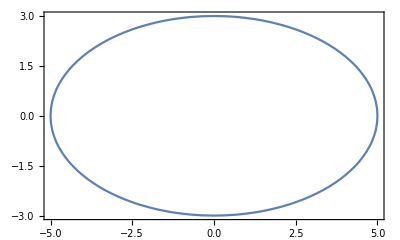

```mathematica
ellipseEq[5,3]
```

## Using Solve eq

```mathematica
sols[a_,b_]:=y/.Solve[x^2/a^2+y^2/b^2==1,y];
ellipseSolve[a_,b_]:=Plot[y/.Solve[x^2/a^2+y^2/b^2==1,y],{x,-1.1a,1.1a},AspectRatio->Automatic];
```

```mathematica
Solve[x^2/a^2+y^2/b^2==1,y]
```

{{y→-(b √(a^2-x^2))/a},{y→(b √(a^2-x^2))/a}}

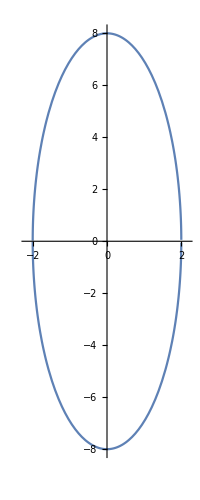

```mathematica
ellipseSolve[2,8]
```

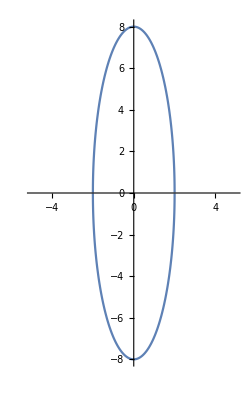

```mathematica
Plot[Sequence@@sols[2,8],{x,-5,5},AspectRatio->Automatic]
```

## Constants

## Defining the inertial terms

```mathematica
Afct[spin_,j_,a1_,a2_,theta_]:=a2(1-(j*Sin[theta])/spin)-a1;
ufct[spin_,j_,a1_,a2_,a3_,theta_]:=(a3-a1)/Afct[spin,j,a1,a2,theta];
v0fct[spin_,j_,a1_,a2_,theta_]:=-(a1*j*Cos[theta])/Afct[spin,j,a1,a2,theta];
```

## General expression for the energy function

```mathematica
Hclassic[r_,theta_,fi_]:=x2[r,theta,fi]^2+u[r] x3[r,theta,fi]^2+2*v0[r]*x1[r,theta,fi];
```

## 2-axis quantization - ℐ_2-> maximal MOI

## Constants

```mathematica
A1=6;
A2=1;
A3=3;
spinvalue=2;
θ=30*π/180;
j=11/2;
(*declare the spherical values*)
rSphere=2;
θSphere=π/6;
ϕSphere=π/9;
```

```mathematica
x1[r_,theta_,fi_]:=r Sin[theta]Cos[fi];
x2[r_,theta_,fi_]:=r Cos[theta];
x3[r_,theta_,fi_]:=r Sin[theta]Sin[fi];
u[spin_]:=N[ufct[spin,j,A1,A2,A3,θ]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,θ]];
Print[u[spinvalue]," ",v0[spinvalue]]
Print[N[x1[rSphere,θSphere,ϕSphere]]," ",N[x2[rSphere,θSphere,ϕSphere]]," ",N[x3[rSphere,θSphere,ϕSphere]]]
```

0.470588 4.48296

0.939693 1.73205 0.34202

```mathematica
Hprime2[spin_,x2_,fi2_]:=x2^2(1-u[spin] Cos[fi2]^2-v0[spin]/spin Sin[fi2])+u[spin] spin^2 Cos[fi2]^2+2v0[spin]*spin*Sin[fi2];
Print[Hclassic[rSphere,θSphere,ϕSphere]," ",Hprime2[rSphere,x2[rSphere,θSphere,ϕSphere],ϕSphere]]
```

11.4802 7.24869

## 3-axis quantization - ℐ_3-> maximal MOI

## Constants

```mathematica
A1=6;
A2=3;
A3=1;
spinvalue=2;
θ=30*π/180;
j=11/2;
(*declare the spherical values*)
rSphere=2;
θSphere=π/6;
ϕSphere=π/9;
```

```mathematica
x1[r_,theta_,fi_]:=r Sin[theta]Cos[fi];
x3[r_,theta_,fi_]:=r Cos[theta];
x2[r_,theta_,fi_]:=r Sin[theta]Sin[fi];
u[spin_]:=N[ufct[spin,j,A1,A2,A3,θ]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,θ]];
Print[u[spinvalue]," ",v0[spinvalue]]
Print[N[x1[rSphere,θSphere,ϕSphere]]," ",N[x2[rSphere,θSphere,ϕSphere]]," ",N[x3[rSphere,θSphere,ϕSphere]]]
```

0.701754 4.01107

0.939693 0.34202 1.73205

```mathematica
Hprime3[spin_,x3_,fi3_]:=x3^2(u[spin]-Sin[fi3]^2-v0[spin]/spin Cos[fi3])+spin^2 Sin[fi3]^2+2v0[spin]spin*Cos[fi3];
Print[Hclassic[rSphere,θSphere,ϕSphere]," ",Hprime3[rSphere,x3[rSphere,θSphere,ϕSphere],ϕSphere]]
```

9.76058 11.6452

## 1-axis quantization - ℐ_1-> maximal MOI

## Constants

```mathematica
A1=1;
A2=3;
A3=6;
spinvalue=2;
θ=30*π/180;
j=11/2;
(*declare the spherical values*)
rSphere=2;
θSphere=π/6;
ϕSphere=π/9;
```

```mathematica
x2[r_,theta_,fi_]:=r Sin[theta]Cos[fi];
x1[r_,theta_,fi_]:=r Cos[theta];
x3[r_,theta_,fi_]:=r Sin[theta]Sin[fi];
u[spin_]:=N[ufct[spin,j,A1,A2,A3,θ]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,θ]];
Print[u[spinvalue]," ",v0[spinvalue]]
Print[N[x1[rSphere,θSphere,ϕSphere]]," ",N[x2[rSphere,θSphere,ϕSphere]]," ",N[x3[rSphere,θSphere,ϕSphere]]]
```

-2.35294 2.24148

1.73205 0.939693 0.34202

```mathematica
Hprime1[spin_,x1_,fi1_]:=(Cos[fi1]^2+u[spin] Sin[fi1]^2)(spin^2-x1^2)+2*v0[spin]*x1;
Print[Hclassic[rSphere,θSphere,ϕSphere]," ",Hprime1[rSphere,x1[rSphere,θSphere,ϕSphere],ϕSphere]]
```

8.37249 8.37249